```mathematica
map:={{1,0,cx},{0,1,cy},{0,0,1}} . {{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}.{{rx,0,0},{0,ry,0},{0,0,1}}
```

```mathematica
form=map.{{Cos[θ]},{Sin[θ]},{1}}
```

{{cx+rx Cos[θ] Cos[ϕ]-ry Sin[θ] Sin[ϕ]},{cy+ry Cos[ϕ] Sin[θ]+rx Cos[θ] Sin[ϕ]},{1}}

```mathematica
(* plain ellipse *)
```

```mathematica
f[θ_,cx_,cy_,rx_,ry_,ϕ_]:={cx+rx Cos[θ] Cos[ϕ]-ry Sin[θ] Sin[ϕ],cy+ry Cos[ϕ] Sin[θ]+rx Cos[θ] Sin[ϕ]}
```

```mathematica
(* normal curve *)
```

```mathematica
fp[θ_,rx_,ry_,ϕ_]:={-rx Cos[ϕ] Sin[θ]-ry Cos[θ] Sin[ϕ],ry Cos[θ] Cos[ϕ]-rx Sin[θ] Sin[ϕ]}
```

```mathematica
(* offset curve *)
```

```mathematica
off[θ_,cx_,cy_,rx_,ry_,ϕ_,d_]:=f[θ,cx,cy,rx,ry,ϕ]+Normalize[{fp[θ,rx,ry,ϕ][[2]],-fp[θ,rx,ry,ϕ][[1]]}]*d
```

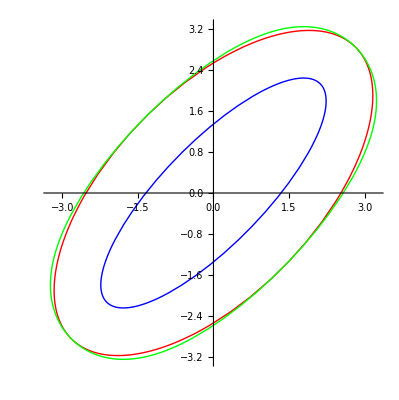

```mathematica
Show[ParametricPlot[f[θ,0,0,3,1,π/4],{θ,0,2*π},PlotStyle->Blue],ParametricPlot[f[θ,0,0,4,2,π/4],{θ,0,2*π},PlotStyle->Red],ParametricPlot[off[θ,0,0,3,1,π/4,1],{θ,0,2*π},PlotStyle->Green],PlotRange->All]
```